```mathematica
maxPotPos=10;
voltRef=5;
res=100;
rise=1;
fall=2;

(* Find the peak position at pot pos (x^2 curve) *)
PPatCP[pos_]:=Module[{},
If[pos<maxPotPos/2,
peak=(pos^2/(maxPotPos/2))*(res/maxPotPos),
peak=res-((maxPotPos-pos)^2/(maxPotPos/2))*(res/maxPotPos)];
peak
];

PPatCP[9]
```

98

```mathematica
percentFall=60;

GetCutoffVolt[curpos_,percentfall_]:=Module[{},
voltPrStep=voltRef/percentfall;
If[res-PPatCP[curpos]-percentfall<0,
cutoff=(voltPrStep*Abs[res-PPatCP[curpos]-percentfall])^2/voltRef,cutoff=0];
cutoff
]

N[GetCutoffVolt[9.9, percentFall]]
```

4.99667

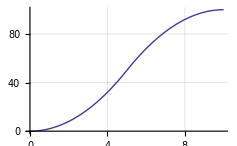

```mathematica
Plot[PPatCP[x], {x, 0, maxPotPos}, 
GridLines->Automatic, GridLinesStyle->LightGray]
```

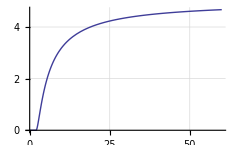

```mathematica
Plot[GetCutoffVolt[9,x], {x, 0, 60}, 
GridLines->Automatic, GridLinesStyle->LightGray]
```